```mathematica
Calculation of constraints on the scattering cross section of DM particles on an electron of an argon atom
```

```mathematica
(ver 0.1, author: Nikita  Levashko, email:nikstar2010@mail.ru, if you notice errors or you have suggestions for improving the code,feel free to write me an email  )
```

```mathematica
1.Minimum velocity of DM particle
```

```mathematica
SetDirectory[NotebookDirectory[]];
c=299792458; (*in m/s*)
Vmin[q1_?NumericQ,Ebound_?NumericQ,Eer_?NumericQ,mmx_?NumericQ]:=((Ebound+Eer)/(q1*10^3)+(q1*10^3)/(2mmx*10^6)); (* minimum velocity of dm particle in c *)
```

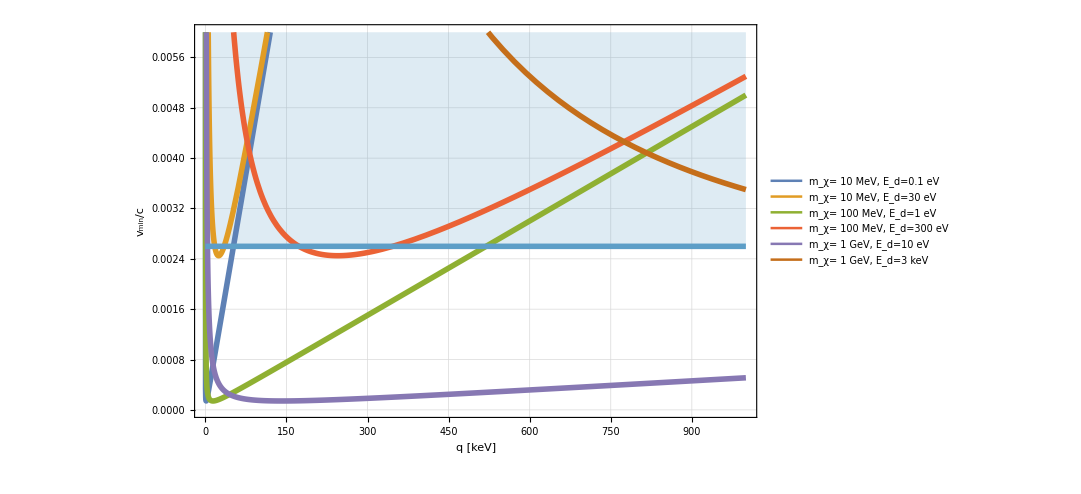

```mathematica
N1=Plot[{Vmin[q1,0.1,0,10],Vmin[q1,30,0,10],Vmin[q1,1,0,100],Vmin[q1,300,0,100],Vmin[q1,10,0,1000],Vmin[q1,3000,0,1000],(vesc+vE)*1000/c},{q1,0,1000},PlotLegends->Placed[LineLegend[{"m_χ= 10 MeV, E_d=0.1 eV","m_χ= 10 MeV, E_d=30 eV","m_χ= 100 MeV, E_d=1 eV","m_χ= 100 MeV, E_d=300 eV","m_χ= 1 GeV, E_d=10 eV","m_χ= 1 GeV, E_d=3 keV"},LegendLayout->"Column"],{Scaled[{0.17,0.75}],{0,0.5}}], ImageSize->800,PlotRange->{0,0.006},Frame->True,Background->White,FrameLabel->{"q [keV]","v_min/c"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing],Filling->{1->None,2->None,3->None,4->None,5->None,6->None,7->Top}]
```

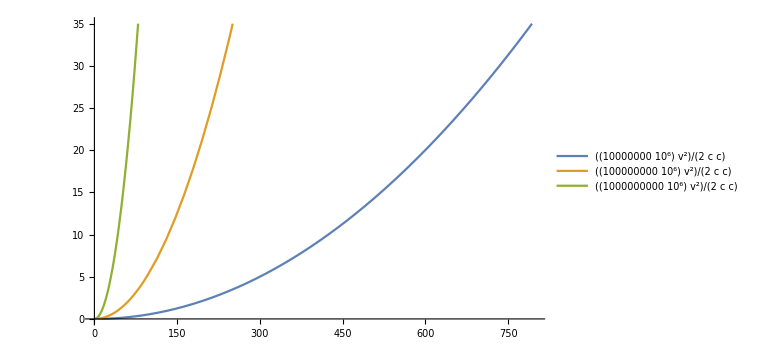

```mathematica
Plot[{((10000000*10^6)/(2*c*c))*v^2,((100000000*10^6)/(2*c*c))*v^2,((1000000000*10^6)/(2*c*c))*v^2},{v,0,800},PlotRange->{0,35},PlotLegends->"Expressions",ImageSize->Large]
```

```mathematica
2.DM velocity distribution and mean inverse speed
```

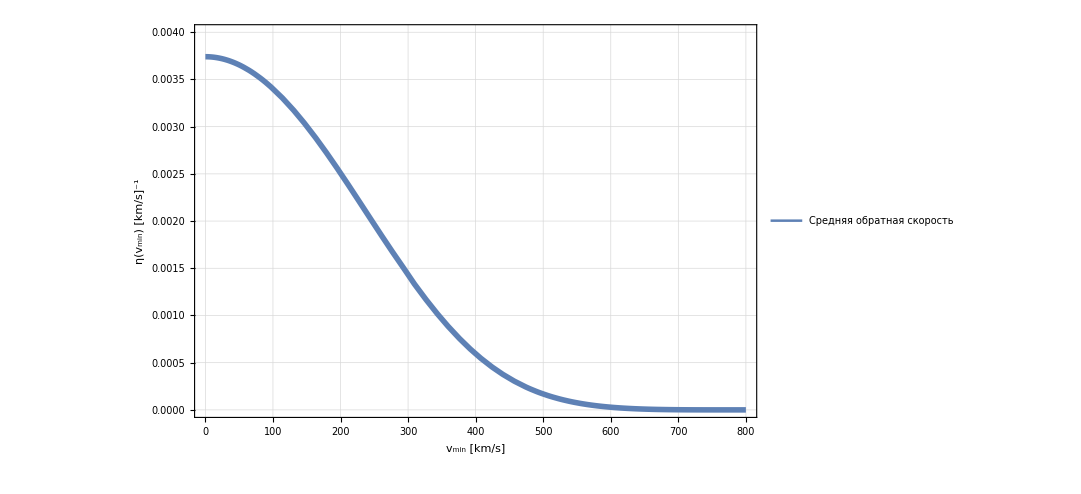

```mathematica
vesc=544; (*escape velocity in km/s*)
v0=220;(*mean velocity in km/s*)
vE=235;(*Earth velocity in km/s*)
xesc=vesc/v0;
xe=vE/v0;
xmin[q1_?NumericQ,Ebound_?NumericQ,Eer_?NumericQ,mmx_?NumericQ]:=Vmin[q1,Ebound,Eer,mmx]/v0;
Norma=Pi^(3/2)*v0^3(Erf[xesc]-4/Pi^(1/2)*ⅇ^(-xesc^2)(xesc/2+xesc^3/3)); (*normalization factor*)
f1[xmin_?NumericQ]:=(Pi^(3/2)*v0^2)/(2Norma xe)(Erf[xe+xmin]-Erf[xmin-xe]-(4xe)/Pi^(1/2)ⅇ^(-xesc^2)(1+xesc^2-xe^2/3-xmin^3));
f2[xmin_?NumericQ]:=(Pi^(3/2)*v0^2)/(2Norma xe)(Erf[xesc]+Erf[-xmin+xe]-2/Pi^(1/2)ⅇ^(-xesc^2)(xesc+xe-xmin-1/3(xe-2xesc-xmin)(xesc+xe-xmin)^2));
f3[xmin_?NumericQ]:=1/(v0 xe);
f4[xmin_?NumericQ]:=0;
Psi[xmin_?NumericQ]:=Piecewise[{{f1[xmin],0<=xmin<xesc-xe},{f2[xmin],xesc-xe≤xmin<xesc+xe},{f4[xmin],xesc+xe<xmin}}];
Psix[v_?NumericQ]:=Psi[v/v0];
PsixoS[v_?NumericQ]:=Psix[v*c*0.001];(* making argument of dunction in appropriate form*)
N2=Plot[Psix[x],{x,0,800},PlotLegends->Placed[LineLegend[{"Mean inverse speed"},LegendLayout->"Column"],{Scaled[{0.47,0.75}],{0,0.5}}], ImageSize->800,PlotRange->{0,0.004},Frame->True,Background->White,FrameLabel->{"v_min [km/s]","η(v_min) [km/s]^-1"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]]
Plot[Psix[x],{x,0,800}]
Plot[PsixoS[x],{x,0,0.002},PlotRange->{0,0.004}]
```

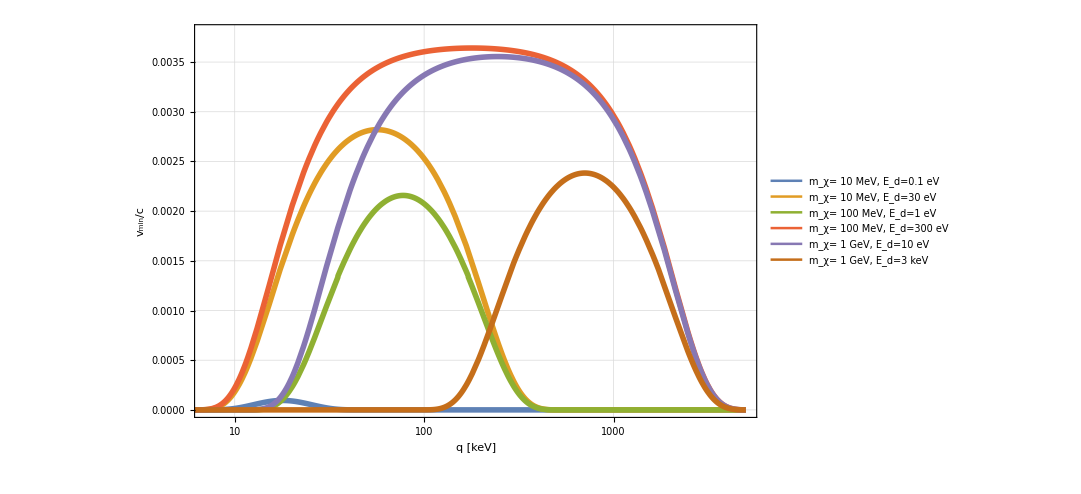

```mathematica
N3=LogLinearPlot[{PsixoS[Vmin[q1,16,0,10]],PsixoS[Vmin[q1,16,0,100]],PsixoS[Vmin[q1,30,0,100]],PsixoS[Vmin[q1,16,0,1000]],PsixoS[Vmin[q1,30,0,1000]],PsixoS[Vmin[q1,249,0,1000]]},{q1,0,5000},PlotLegends->LineLegend[{"m_χ= 10 MeV, E_d=0.1 eV","m_χ= 10 MeV, E_d=30 eV","m_χ= 100 MeV, E_d=1 eV","m_χ= 100 MeV, E_d=300 eV","m_χ= 1 GeV, E_d=10 eV","m_χ= 1 GeV, E_d=3 keV"},LegendLayout->"Column"], ImageSize->800,PlotRange->{{7,5000},{0,0.0038}},Frame->True,Background->White,FrameLabel->{"q [keV]","v_min/c"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]]
Plot[{PsixoS[Vmin[5,x,0,10]],PsixoS[Vmin[5,x,0,100]],PsixoS[Vmin[5,x,0,1000]]},{x,0,10},PlotLegends->"Expressions"]
Plot[{PsixoS[Vmin[20,x,0,10]],PsixoS[Vmin[20,x,0,100]],PsixoS[Vmin[50,x,0,100]],PsixoS[Vmin[20,x,0,1000]],PsixoS[Vmin[50,x,0,1000]],PsixoS[Vmin[100,x,0,1000]]},{x,0,200},PlotLegends->"Expressions",FrameLabel->{"q [keV]","η(v_min) [km/s]^-1"}]
```

```mathematica
3.Electron wavefunctions in bound state
```

```mathematica
Cs={{0.316405, 0.079148, 0.035512},{0.542760, -0.507823, -0.181267},{0.167691, 0.059900, 0.026500},{0.000408,-0.026389, 0.006280},{0.002431, 0.832638, 0.111836},{-0.000861, 0.295522,0.385604},{-0.000422, 0.000217, 0.000070},{0.000066, 0.002203, -0.376901},{-0.000061,0.001423, -0.593561},{0.000009, 0.000186, -0.229971}};
Zs={25.5708, 15.6262, 22.3994, 10.5300, 7.0534, 5.4120, 46.7052, 3.7982, 2.5495, 1.7965};
Ns={1,1,2,2,2,2,3,3,3,3};
Cp={{0.002436,0.001854},{-0.114774, -0.042064},{-0.503175, -0.095603},{-0.427033, -0.194233},{0.009669, 0.005891},{-0.004825,0.366141},{0.000231,0.526490},{-0.000098, 0.249866}};
Zp={26.6358,12.7337, 7.3041, 5.3353, 20.7765, 3.3171, 2.0947, 1.3780};
Np={2,2,2,2,3,3,3,3};
```

```mathematica
a=52.917720859*10^(-10);(*bohr radius in cm *)
ap=0.268;(* bohr radius in keV^-1 *)
R1s[r_?NumericQ]:=a^(-3/2)Sum[Cs[[j,1]]*(((2*Zs[[j]])^(Ns[[j]]+1/2))/Sqrt[(2*Ns[[j]])!])*((r/a)^(Ns[[j]]-1))*Exp[-Zs[[j]]*r/a],{j,10}];
R2s[r_?NumericQ]:=a^(-3/2)Sum[Cs[[j,2]]*(((2*Zs[[j]])^(Ns[[j]]+1/2))/Sqrt[(2*Ns[[j]])!])*((r/a)^(Ns[[j]]-1))*Exp[-Zs[[j]]*r/a],{j,10}];
R3s[r_?NumericQ]:=a^(-3/2)Sum[Cs[[j,3]]*(((2*Zs[[j]])^(Ns[[j]]+1/2))/Sqrt[(2*Ns[[j]])!])*((r/a)^(Ns[[j]]-1))*Exp[-Zs[[j]]*r/a],{j,10}];
R2p[r_?NumericQ]:=a^(-3/2)Sum[Cp[[j,1]]*(((2*Zp[[j]])^(Np[[j]]+1/2))/Sqrt[(2*Np[[j]])!])*((r/a)^(Np[[j]]-1))*Exp[-Zp[[j]]*r/a],{j,8}];
R3p[r_?NumericQ]:=a^(-3/2)Sum[Cp[[j,2]]*(((2*Zp[[j]])^(Np[[j]]+1/2))/Sqrt[(2*Np[[j]])!])*((r/a)^(Np[[j]]-1))*Exp[-Zp[[j]]*r/a],{j,8}];
Nors=0.886226216583027;(* Normalization factor for s shells *)
Norp=1.329339686566492;(* Normalization factor for p shells *)
X1s[k_?NumericQ]:=(1/Nors)*Sum[Cs[[j,1]]*(2^(Ns[[j]]))*((2*Pi*ap/Zs[[j]])^1.5)*(((1+Ns[[j]])!)/Sqrt[(2*Ns[[j]])!])*Hypergeometric2F1[1.+Ns[[j]]/2,1.5+Ns[[j]]/2,1.5,-(k*ap/Zs[[j]])^2],{j,10}];
X2s[k_?NumericQ]:=(1/Nors)*Sum[Cs[[j,2]]*(2^(Ns[[j]]))*((2*Pi*ap/Zs[[j]])^1.5)*(((1+Ns[[j]])!)/Sqrt[(2*Ns[[j]])!])*Hypergeometric2F1[1.+Ns[[j]]/2,1.5+Ns[[j]]/2,1.5,-(k*ap/Zs[[j]])^2],{j,10}];
X3s[k_?NumericQ]:=(1/Nors)*Sum[Cs[[j,3]]*(2^(Ns[[j]]))*((2*Pi*ap/Zs[[j]])^1.5)*(((1+Ns[[j]])!)/Sqrt[(2*Ns[[j]])!])*Hypergeometric2F1[1.+Ns[[j]]/2,1.5+Ns[[j]]/2,1.5,-(k*ap/Zs[[j]])^2],{j,10}];
X2p[k_?NumericQ]:=(1/Norp)*Sum[Cp[[j,1]]*(2^(Np[[j]]-1))*((2*Pi*ap/Zp[[j]])^1.5)*(I*k*ap/Zp[[j]])*(((2+Np[[j]])!)/Sqrt[(2*Np[[j]])!])*Hypergeometric2F1[1.5+Np[[j]]/2,2.+Np[[j]]/2,2.5,-(k*ap/Zp[[j]])^2],{j,8}];
X3p[k_?NumericQ]:=(1/Norp)*Sum[Cp[[j,2]]*(2^(Np[[j]]-1))*((2*Pi*ap/Zp[[j]])^1.5)*(I*k*ap/Zp[[j]])*(((2+Np[[j]])!)/Sqrt[(2*Np[[j]])!])*Hypergeometric2F1[1.5+Np[[j]]/2,2.+Np[[j]]/2,2.5,-(k*ap/Zp[[j]])^2],{j,8}];
```

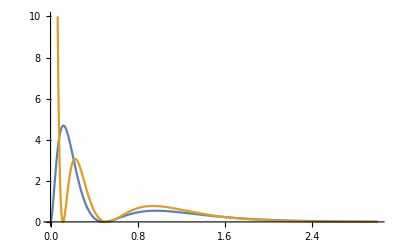

```mathematica
Plot[{Abs[R3p[r*a]*R3p[r*a]]*a^3,Abs[R3s[r*a]*R3s[r*a]]*a^3},{r,0,3},PlotRange->{0,10}]
```

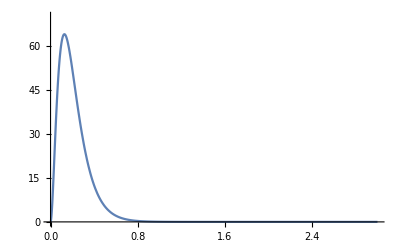

```mathematica
Plot[Abs[R2p[r*a]*R2p[r*a]]*a^3,{r,0,3},PlotRange->{0,70}]
```

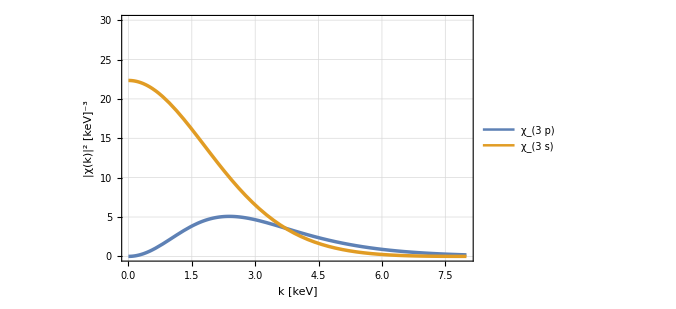

```mathematica
N4=Plot[{Abs[X3p[k]]*Abs[X3p[k]],Abs[X3s[k]*X3s[k]]},{k,0,8},PlotRange->{0,30},PlotLegends->Placed[LineLegend[{"χ_(3  p)","χ_(3  s)"},LegendLayout->"Column"],{Scaled[{0.47,0.75}],{0,0.5}}], ImageSize->500,PlotRange->{0,0.004},Frame->True,Background->White,FrameLabel->{"k [keV]","|χ(k)|^2 [keV]^-3"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]]
```

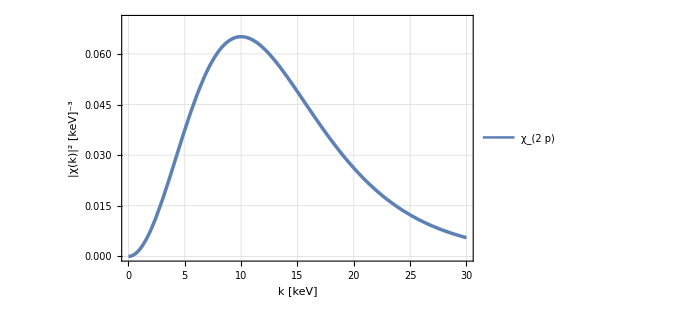

```mathematica
N5=Plot[Abs[X2p[k]*X2p[k]],{k,0,30},PlotRange->{0,0.07},PlotLegends->Placed[LineLegend[{"χ_(2  p)"},LegendLayout->"Column"],{Scaled[{0.57,0.75}],{0,0.5}}], ImageSize->500,PlotRange->{0,0.004},Frame->True,Background->White,FrameLabel->{"k [keV]","|χ(k)|^2 [keV]^-3"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]]
```

```mathematica
4.Electron binding energy and Fermi factor
```

```mathematica
E1s=3206.2;
E2s=324.2;
E2p=247.74;
E3s=34.76;
E3p=16.08;
Z1s=Sqrt[E1s/13.6] ; 
Z2s=Sqrt[E2s/13.6]*2;
Z2p=Sqrt[E2p/13.6]*2;
Z3s=Sqrt[E3s/13.6]*3;
Z3p=Sqrt[E3p/13.6]*3;

Fff[k1_?NumericQ,Z_?NumericQ]:=((2 Pi Z)/(k1*ap))*1/(1-Exp[-(2 Pi Z)/(k1*ap)]); 
me=0.51099895; (* electron mass in MeV*)
```

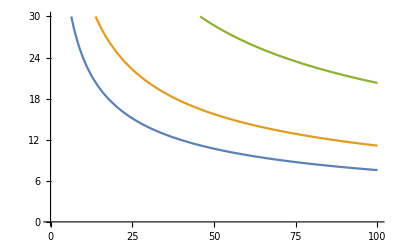

```mathematica
Plot[{Fff[Sqrt[2*me*Ee],3.26],Fff[Sqrt[2*me*Ee],4.80],Fff[Sqrt[2*me*Ee],8.75]},{Ee,0,100},PlotRange->{0,30}]
```

```mathematica
5.Ionization formfactors
```

```mathematica
Form1s[k_?NumericQ,q_?NumericQ]:=Fff[k,Z1s]*((k^2)/(4*(Pi^3)*q))*NIntegrate[x*Abs[X1s[x]]^2,{x,Abs[k-q],k+q},Method->{Automatic,"SymbolicProcessing"->0.3}];
Form2s[k_?NumericQ,q_?NumericQ]:=Fff[k,Z2s]*((k^2)/(4*(Pi^3)*q))*NIntegrate[x*Abs[X2s[x]]^2,{x,Abs[k-q],k+q},Method->{Automatic,"SymbolicProcessing"->0.3}];
Form3s[k_?NumericQ,q_?NumericQ]:=Fff[k,Z3s]*((k^2)/(4*(Pi^3)*q))*NIntegrate[x*Abs[X3s[x]]^2,{x,Abs[k-q],k+q},Method->{Automatic,"SymbolicProcessing"->0.3}];
Form2p[k_?NumericQ,q_?NumericQ]:=Fff[k,Z2p]*((3*k^2)/(4*(Pi^3)*q))*NIntegrate[x*Abs[X2p[x]]^2,{x,Abs[k-q],k+q},Method->{Automatic,"SymbolicProcessing"->0.3}];
Form3p[k_?NumericQ,q_?NumericQ]:=Fff[k,Z3p]*((3*k^2)/(4*(Pi^3)*q))*NIntegrate[x*Abs[X3p[x]]^2,{x,Abs[k-q],k+q},Method->{Automatic,"SymbolicProcessing"->0.3}];
```

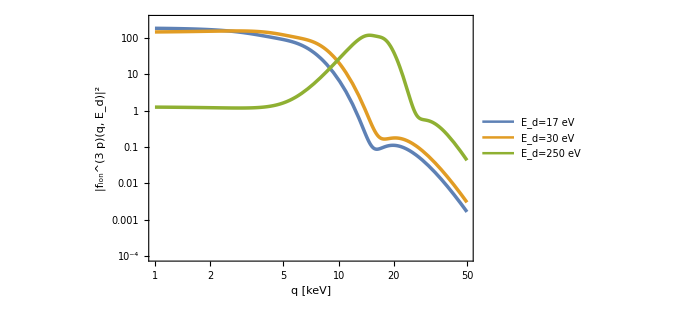

```mathematica
N6=LogLogPlot[{Form3p[Sqrt[2*me*17],q],Form3p[Sqrt[2*me*30],q],Form3p[Sqrt[2*me*250],q]},{q,1,50},PlotRange->{10^-4,300},PlotLegends->Placed[LineLegend[{"E_d=17 eV","E_d=30 eV","E_d=250 eV"},LegendLayout->"Column"],{Scaled[{0.27,0.35}],{0,0.5}}], ImageSize->500,Frame->True,Background->White,FrameLabel->{"q [keV]","|f_ion^(3  p)(q, E_d)|^2"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]]
```

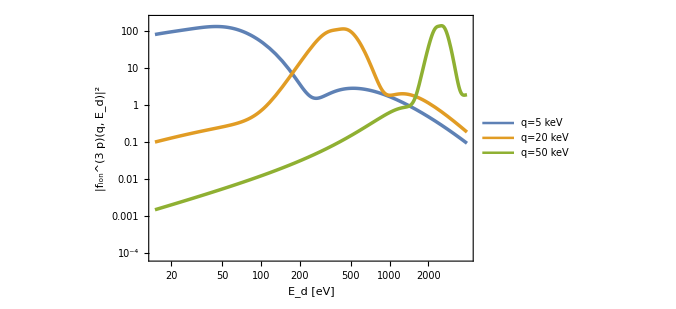

```mathematica
N7=LogLogPlot[{Form3p[Sqrt[2*me*Eer],5],Form3p[Sqrt[2*me*Eer],20],Form3p[Sqrt[2*me*Eer],50]},{Eer,15,4000},PlotRange->{10^-4.1,200},PlotLegends->Placed[LineLegend[{"q=5 keV","q=20 keV","q=50 keV"},LegendLayout->"Column"],{Scaled[{0.57,0.29}],{0,0.5}}], ImageSize->500,Frame->True,Background->White,FrameLabel->{"E_d [eV]","|f_ion^(3  p)(q, E_d)|^2"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]]
```

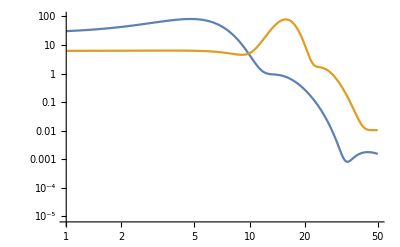

```mathematica
LogLogPlot[{Form3s[Sqrt[2*me*30],q],Form3s[Sqrt[2*me*250],q]},{q,1,50},PlotRange->{10^-5.2,100}]
```

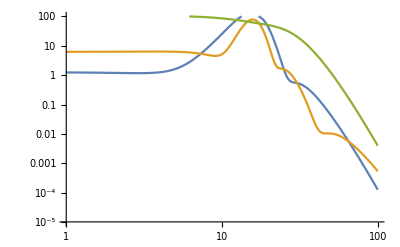

```mathematica
LogLogPlot[{Form3p[Sqrt[2*me*250],q],Form3s[Sqrt[2*me*250],q],Form2p[Sqrt[2*me*250],q]},{q,1,100},PlotRange->{10^-5,100}]
```

```mathematica
6.Some constants and DM formactor
ArA=39.9; (*argon mass in atomic mass unit*)
aem=1.660539*10^-27;(*atomic mass unit in kg*)
evCm=1.97327*10^-5; (*1 ev into cm*)
evS=6.582119*10^-16;(*1 ev into s*)
cmVsec=evS/evCm;(* conversion factor from cm to s *)
MT[A_]:=0.932 A; (* catomic mass unit into GeV *)
ArNth=2.3; (* the number of expected events with a probability level of 90% at zero detected particles *)
Na=6.02 10^23;
alpha=1/137;
mu[mmx_?NumericQ]:=mmx*me/(mmx+me);
Fdm1[q1_?NumericQ]:=1;(*Formfactor of DM in case of heavy mediator*)
Fdm2[q1_?NumericQ]:=(10^6)*((alpha*me)^2)/q1^2;(*Formfactor of DM in case of light mediator*)
Rox=0.4;(*DM density in GeV*)
```

```mathematica
7.Differential rate 
Rate1s[mmx_?NumericQ,Eer_?NumericQ]:=NIntegrate[1/(ArA*aem)(60*60*24)/cmVsec*Form1s[(2*me*Eer)^0.5,q1]*(10^-36)/(mu[mmx]^2) Rox 0.001/(8*mmx)PsixoS[Vmin[q1,E1s,Eer,mmx]]*q1,{q1,0,mmx*10}];
Rate2s[mmx_?NumericQ,Eer_?NumericQ]:=NIntegrate[1/(ArA*aem)(60*60*24)/cmVsec*Form2s[(2*me*Eer)^0.5,q1]*(10^-36)/(mu[mmx]^2) Rox 0.001/(8*mmx)PsixoS[Vmin[q1,E2s,Eer,mmx]]*q1,{q1,0,mmx*10}];
Rate3s[mmx_?NumericQ,Eer_?NumericQ]:=NIntegrate[1/(ArA*aem)(60*60*24)/cmVsec*Form3s[(2*me*Eer)^0.5,q1]*(10^-36)/(mu[mmx]^2) Rox 0.001/(8*mmx)PsixoS[Vmin[q1,E3s,Eer,mmx]]*q1,{q1,0,mmx*10}];
Rate2p[mmx_?NumericQ,Eer_?NumericQ]:=NIntegrate[1/(ArA*aem)(60*60*24)/cmVsec*Form2p[(2*me*Eer)^0.5,q1]*(10^-36)/(mu[mmx]^2) Rox 0.001/(8*mmx)PsixoS[Vmin[q1,E2p,Eer,mmx]]*q1,{q1,0,mmx*10}];
Rate3p[mmx_?NumericQ,Eer_?NumericQ]:=NIntegrate[1/(ArA*aem)(60*60*24)/cmVsec*Form3p[(2*me*Eer)^0.5,q1]*(10^-36)/(mu[mmx]^2) Rox 0.001/(8*mmx)PsixoS[Vmin[q1,E3p,Eer,mmx]]*q1,{q1,0,mmx*10}];
```

```mathematica
Rate1sF[mmx_?NumericQ,Eer_?NumericQ]:=NIntegrate[1/(ArA*aem)(60*60*24)/cmVsec*Form1s[(2*me*Eer)^0.5,q1]*(10^-33)/(mu[mmx]^2) Rox 0.001/(8*mmx)Fdm2[q1]^2PsixoS[Vmin[q1,E1s,Eer,mmx]]*q1,{q1,0,mmx*10}];
Rate2sF[mmx_?NumericQ,Eer_?NumericQ]:=NIntegrate[1/(ArA*aem)(60*60*24)/cmVsec*Form2s[(2*me*Eer)^0.5,q1]*(10^-33)/(mu[mmx]^2) Rox 0.001/(8*mmx)Fdm2[q1]^2PsixoS[Vmin[q1,E2s,Eer,mmx]]*q1,{q1,0,mmx*10}];
Rate3sF[mmx_?NumericQ,Eer_?NumericQ]:=NIntegrate[1/(ArA*aem)(60*60*24)/cmVsec*Form3s[(2*me*Eer)^0.5,q1]*(10^-33)/(mu[mmx]^2) Rox 0.001/(8*mmx)Fdm2[q1]^2PsixoS[Vmin[q1,E3s,Eer,mmx]]*q1,{q1,0,mmx*10}];
Rate2pF[mmx_?NumericQ,Eer_?NumericQ]:=NIntegrate[1/(ArA*aem)(60*60*24)/cmVsec*Form2p[(2*me*Eer)^0.5,q1]*(10^-33)/(mu[mmx]^2) Rox 0.001/(8*mmx)Fdm2[q1]^2PsixoS[Vmin[q1,E2p,Eer,mmx]]*q1,{q1,0,mmx*10}];
Rate3pF[mmx_?NumericQ,Eer_?NumericQ]:=NIntegrate[1/(ArA*aem)(60*60*24)/cmVsec*Form3p[(2*me*Eer)^0.5,q1]*(10^-33)/(mu[mmx]^2) Rox 0.001/(8*mmx)Fdm2[q1]^2PsixoS[Vmin[q1,E3p,Eer,mmx]]*q1,{q1,0,mmx*10}];
```

```mathematica
Gra13p=Table[{Ee,Rate3p[100,Ee]},{Ee,0.1,500,10}];
Gra12p=Table[{Ee,Rate2p[100,Ee]},{Ee,0.1,500,10}];
Gra13s=Table[{Ee,Rate3s[100,Ee]},{Ee,0.1,500,10}];
Gra23p=Table[{Ee,Rate3p[1000,Ee]},{Ee,0.1,500,10}];
Gra22p=Table[{Ee,Rate2p[1000,Ee]},{Ee,0.1,500,10}];
Gra23s=Table[{Ee,Rate3s[1000,Ee]},{Ee,0.1,500,10}];
```

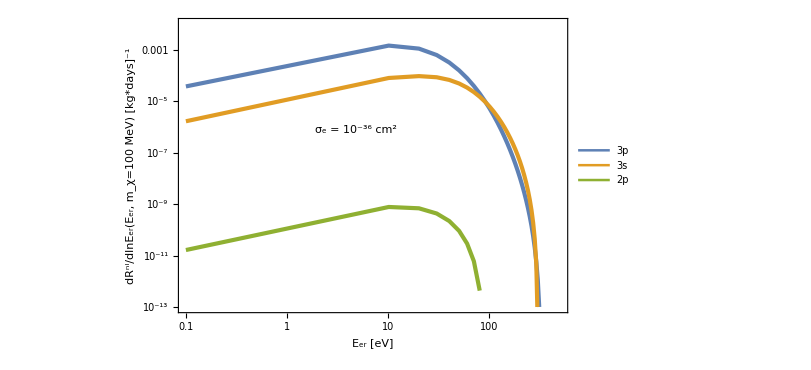

```mathematica
N8=Legended[ListLogLogPlot[{Gra13p,Gra13s,Gra12p},Joined->True,PlotRange->{{0.1,500},{10^-13,10^-2}},PlotLegends->Placed[LineLegend[{"3p","3s","2p"},LegendLayout->"Column"],{Scaled[{0.15,0.5}],{0,0.5}}], ImageSize->600,Frame->True,Background->White,FrameLabel->{"E_er [eV]","dR^nl/dlnE_er(E_er, m_χ=100 MeV) [kg*days]^-1"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]],Placed[Text["σ_e = 10^-36 cm^2"],{Scaled[{0.35,0.62}],{0,0.5}}]]
```

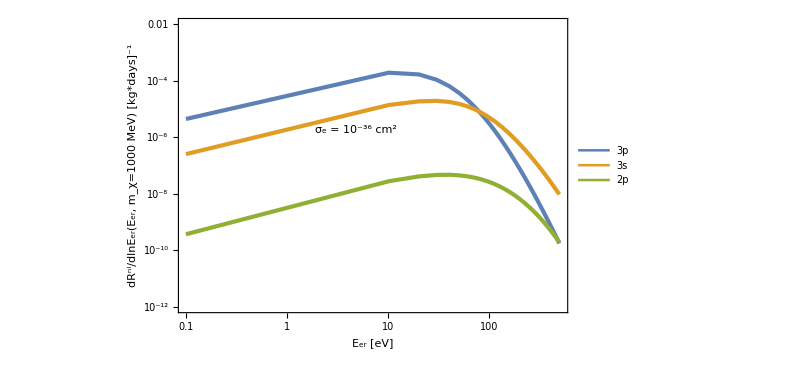

```mathematica
N9=Legended[ListLogLogPlot[{Gra23p,Gra23s,Gra22p},Joined->True,PlotRange->{{0.1,500},{10^-12,10^-2}},PlotLegends->Placed[LineLegend[{"3p","3s","2p"},LegendLayout->"Column"],{Scaled[{0.55,0.25}],{0,0.5}}], ImageSize->600,Frame->True,Background->White,FrameLabel->{"E_er [eV]","dR^nl/dlnE_er(E_er, m_χ=1000 MeV) [kg*days]^-1"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]],Placed[Text["σ_e = 10^-36 cm^2"],{Scaled[{0.35,0.62}],{0,0.5}}]]
```

```mathematica
Pra1=Table[{10^x,Rate3p[10,10^x]+Rate2p[10,10^x]+Rate3s[10,10^x]},{x,-1,3,0.05}];
```

```mathematica
Pra2=Table[{10^x,Rate3p[100,10^x]+Rate2p[100,10^x]+Rate3s[100,10^x]},{x,-1,3,0.1}];
Pra3=Table[{10^x,Rate3p[1000,10^x]+Rate2p[1000,10^x]+Rate3s[1000,10^x]},{x,-1,3,0.1}];
```

```mathematica
Pra4=Table[{10^x,Rate3pF[10,10^x]+Rate2pF[10,10^x]+Rate3sF[10,10^x]},{x,-3,3,0.05}];
```

```mathematica
Pra5=Table[{10^x,Rate3pF[100,10^x]+Rate2pF[100,10^x]+Rate3sF[100,10^x]},{x,-1,3,0.1}];
Pra6=Table[{10^x,Rate3pF[1000,10^x]+Rate2pF[1000,10^x]+Rate3sF[1000,10^x]},{x,-1,3,0.1}];
```

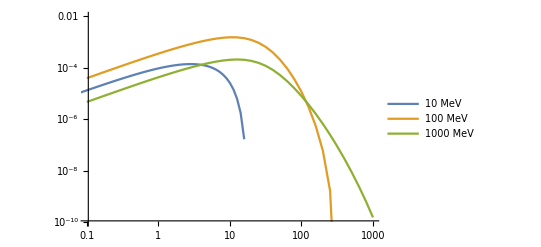

```mathematica
ListLogLogPlot[{Pra1,Pra2,Pra3},PlotLegends->{"10 MeV","100 MeV","1000 MeV"},Joined->True,PlotRange->{{0.1,1000},{10^-10,10^-2}}]
```

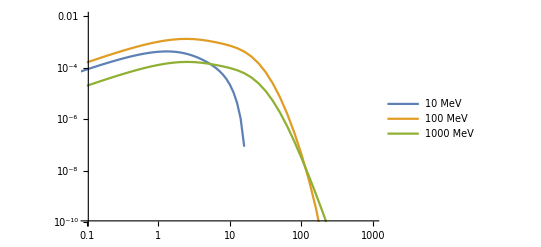

```mathematica
ListLogLogPlot[{Pra4,Pra5,Pra6},PlotLegends->{"10 MeV","100 MeV","1000 MeV"},Joined->True,PlotRange->{{0.1,1000},{10^-10,10^-2}}]
```

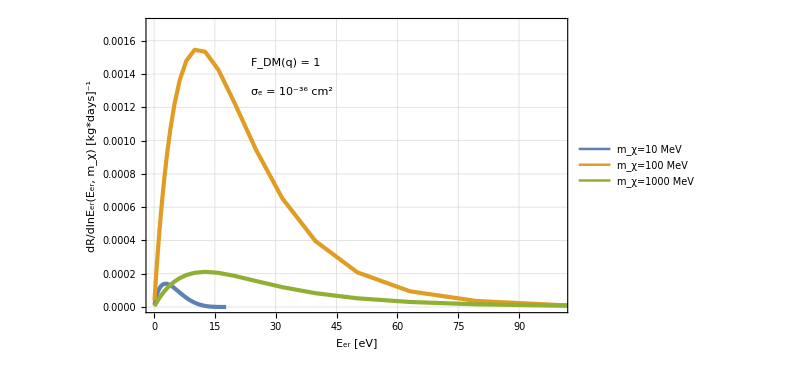

```mathematica
N10=Legended[Legended[ListPlot[{Pra1,Pra2,Pra3},Joined->True,PlotRange->{{0,100},{10^-10,0.0017}},PlotLegends->Placed[LineLegend[{"m_χ=10 MeV","m_χ=100 MeV","m_χ=1000 MeV"},LegendLayout->"Column"],{Scaled[{0.55,0.55}],{0,0.5}}], ImageSize->600,Frame->True,Background->White,FrameLabel->{"E_er [eV]","dR/dlnE_er(E_er, m_χ) [kg*days]^-1"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]],Placed[Text["σ_e = 10^-36 cm^2"],{Scaled[{0.25,0.75}],{0,0.5}}]],Placed[Text["F_DM(q) = 1"],{Scaled[{0.25,0.85}],{0,0.5}}]]
```

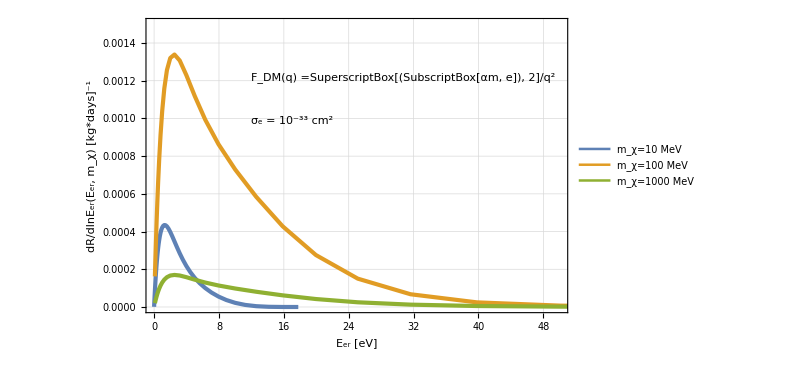

```mathematica
N11=Legended[Legended[ListPlot[{Pra4,Pra5,Pra6},Joined->True,PlotRange->{{0,50},{10^-10,0.0015}},PlotLegends->Placed[LineLegend[{"m_χ=10 MeV","m_χ=100 MeV","m_χ=1000 MeV"},LegendLayout->"Column"],{Scaled[{0.56,0.40}],{0,0.5}}], ImageSize->600,Frame->True,Background->White,FrameLabel->{"E_er [eV]","dR/dlnE_er(E_er, m_χ) [kg*days]^-1"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]],Placed[Text["σ_e = 10^-33 cm^2"],{Scaled[{0.25,0.65}],{0,0.5}}]],Placed[Text["F_DM(q) =SuperscriptBox[(SubscriptBox[αm, e]), 2]/q^2"],{Scaled[{0.25,0.80}],{0,0.5}}]]
```

```mathematica
8.Converting energy to number of electrons
```

```mathematica
ArExp=16660;(* exsposure in kg*days *)
Tacki={{0.27,11.2},{2.82,48}};(*data for interpolation conversion function*)
Func=NonlinearModelFit[Tacki,ak x^bk,{ak,bk},x]
```

FittedModel[25.2318 x^0.620308]

```mathematica
Convert[Ee_?NumericQ]:=25.2318*Ee^(0.620308);
```

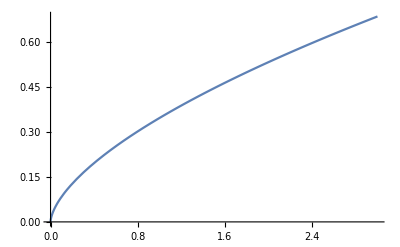

```mathematica
Plot[Convert[Ee/1000],{Ee,0,3}]
```

```mathematica
ArσE5[Ne_]:=0.25 Ne^0.45;
ArσE6[Ne_]:=0.29+0.17*( Ne-1);
G[Ne_,Ne2_]:=1/7 1/(√(2π) ArσE5[Ne2])ⅇ^(-(Ne-Ne2)^2/(2 ArσE5[Ne2]^2))+6/7 1/(√(2π) ArσE6[Ne2])ⅇ^(-(Ne-Ne2)^2/(2 ArσE6[Ne2]^2));(*PMT response function*)
```

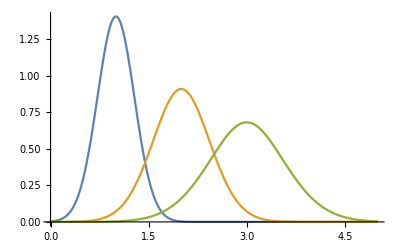

```mathematica
Plot[{G[Ne,1],G[Ne,2],G[Ne,3]},{Ne,0,5}]
```

```mathematica
9.Rate from number of ionized electrons
```

```mathematica
Inert3p[mmx_?NumericQ,Eer_?NumericQ,Ne_?NumericQ,q1_?NumericQ]:=ArExp*1/(ArA*aem)(60*60*24)/cmVsec*Form3p[(2*me*Eer)^0.5,q1]*(10^-36)/(mu[mmx]^2) Rox 0.001/(8*mmx)PsixoS[Vmin[q1,E3p,Eer,mmx]]*q1*G[Ne,Convert[Eer/1000]];
Inert3s[mmx_?NumericQ,Eer_?NumericQ,Ne_?NumericQ,q1_?NumericQ]:=ArExp*1/(ArA*aem)(60*60*24)/cmVsec*Form3s[(2*me*Eer)^0.5,q1]*(10^-36)/(mu[mmx]^2) Rox 0.001/(8*mmx)PsixoS[Vmin[q1,E3s,Eer,mmx]]*q1*G[Ne,Convert[Eer/1000]];
Inert2p[mmx_?NumericQ,Eer_?NumericQ,Ne_?NumericQ,q1_?NumericQ]:=ArExp*1/(ArA*aem)(60*60*24)/cmVsec*Form2p[(2*me*Eer)^0.5,q1]*(10^-36)/(mu[mmx]^2) Rox 0.001/(8*mmx)PsixoS[Vmin[q1,E2p,Eer,mmx]]*q1*G[Ne,Convert[Eer/1000]];
Inert3pF[mmx_?NumericQ,Eer_?NumericQ,Ne_?NumericQ,q1_?NumericQ]:=ArExp*1/(ArA*aem)(60*60*24)/cmVsec*Form3p[(2*me*Eer)^0.5,q1]*(10^-33)/(mu[mmx]^2) *(Fdm2[q1]^2)*Rox 0.001/(8*mmx)PsixoS[Vmin[q1,E3p,Eer,mmx]]*q1*G[Ne,Convert[Eer/1000]];
Inert3sF[mmx_?NumericQ,Eer_?NumericQ,Ne_?NumericQ,q1_?NumericQ]:=ArExp*1/(ArA*aem)(60*60*24)/cmVsec*Form3s[(2*me*Eer)^0.5,q1]*(10^-33)/(mu[mmx]^2)*(Fdm2[q1]^2)* Rox 0.001/(8*mmx)PsixoS[Vmin[q1,E3s,Eer,mmx]]*q1*G[Ne,Convert[Eer/1000]];
Inert2pF[mmx_?NumericQ,Eer_?NumericQ,Ne_?NumericQ,q1_?NumericQ]:=ArExp*1/(ArA*aem)(60*60*24)/cmVsec*Form2p[(2*me*Eer)^0.5,q1]*(10^-33)/(mu[mmx]^2)*(Fdm2[q1]^2)* Rox 0.001/(8*mmx)PsixoS[Vmin[q1,E2p,Eer,mmx]]*q1*G[Ne,Convert[Eer/1000]];
```

```mathematica
Monitor[Nra1=Table[{Ne,NIntegrate[Inert2p[10,Eer,Ne,q1]+Inert3p[10,Eer,Ne,q1]+Inert3s[10,Eer,Ne,q1],{q1,0.01,200},{Eer,0.01,100},PrecisionGoal->2,MinRecursion->2]},{Ne,0.00,15}],Ne];
```

```mathematica
Monitor[Nra2=Table[{Ne,NIntegrate[Inert2p[100,Eer,Ne,q1]+Inert3p[100,Eer,Ne,q1]+Inert3s[100,Eer,Ne,q1],{q1,0.01,400},{Eer,0.01,200},PrecisionGoal->2,MinRecursion->2]},{Ne,0.00,15}],Ne];
```

```mathematica
Monitor[Nra3=Table[{Ne,NIntegrate[Inert2p[1000,Eer,Ne,q1]+Inert3p[1000,Eer,Ne,q1]+Inert3s[1000,Eer,Ne,q1],{q1,0.01,5000},{Eer,0.01,500},PrecisionGoal->2,MinRecursion->2]},{Ne,0.00,15}],Ne];
```

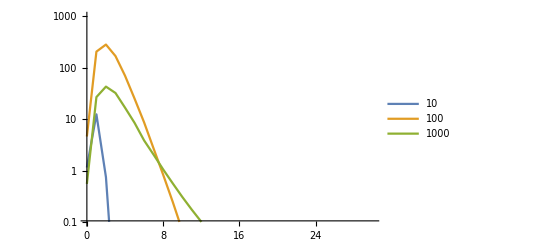

```mathematica
ListLogPlot[{Nra1,Nra2,Nra3},PlotRange->{{0,30},{10^-1,1000}},Joined->True,PlotLegends->{"10","100","1000"}]
```

```mathematica
Monitor[NraF1=Table[{Ne,NIntegrate[Inert2pF[10,Eer,Ne,q1]+Inert3pF[10,Eer,Ne,q1]+Inert3sF[10,Eer,Ne,q1],{q1,0.01,200},{Eer,0.01,100},PrecisionGoal->2,MinRecursion->2]},{Ne,0.00,15}],Ne];
Monitor[NraF2=Table[{Ne,NIntegrate[Inert2pF[100,Eer,Ne,q1]+Inert3pF[100,Eer,Ne,q1]+Inert3sF[100,Eer,Ne,q1],{q1,0.01,400},{Eer,0.01,200},PrecisionGoal->2,MinRecursion->2]},{Ne,0.00,15}],Ne];
Monitor[NraF3=Table[{Ne,NIntegrate[Inert2pF[1000,Eer,Ne,q1]+Inert3pF[1000,Eer,Ne,q1]+Inert3sF[1000,Eer,Ne,q1],{q1,0.01,5000},{Eer,0.01,500},PrecisionGoal->2,MinRecursion->2]},{Ne,0.00,15}],Ne];
```

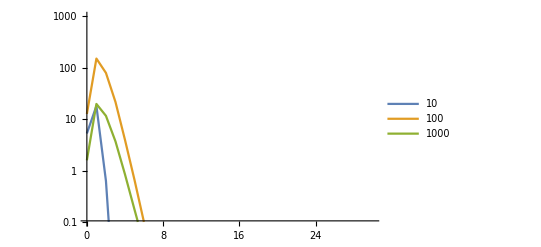

```mathematica
ListLogPlot[{NraF1,NraF2,NraF3},PlotRange->{{0,30},{10^-1,1000}},Joined->True,PlotLegends->{"10","100","1000"}]
```

```mathematica
(*Here we calculate the points in the middle of cell: 0.5, 1.5, etc*)
```

```mathematica
Monitor[PoluNra1=Table[{Ne,NIntegrate[Inert2p[10,Eer,Ne,q1]+Inert3p[10,Eer,Ne,q1]+Inert3s[10,Eer,Ne,q1],{q1,0.01,200},{Eer,0.01,100},PrecisionGoal->2,MinRecursion->2]},{Ne,0.50,15}],Ne];
Monitor[PoluNra2=Table[{Ne,NIntegrate[Inert2p[100,Eer,Ne,q1]+Inert3p[100,Eer,Ne,q1]+Inert3s[100,Eer,Ne,q1],{q1,0.01,400},{Eer,0.01,200},PrecisionGoal->2,MinRecursion->2]},{Ne,0.50,15}],Ne];
Monitor[PoluNra3=Table[{Ne,NIntegrate[Inert2p[1000,Eer,Ne,q1]+Inert3p[1000,Eer,Ne,q1]+Inert3s[1000,Eer,Ne,q1],{q1,0.01,5000},{Eer,0.01,500},PrecisionGoal->2,MinRecursion->2]},{Ne,0.50,15}],Ne];
Monitor[PoluNraF1=Table[{Ne,NIntegrate[Inert2pF[10,Eer,Ne,q1]+Inert3pF[10,Eer,Ne,q1]+Inert3sF[10,Eer,Ne,q1],{q1,0.01,200},{Eer,0.01,100},PrecisionGoal->2,MinRecursion->2]},{Ne,0.50,15}],Ne];
Monitor[PoluNraF2=Table[{Ne,NIntegrate[Inert2pF[100,Eer,Ne,q1]+Inert3pF[100,Eer,Ne,q1]+Inert3sF[100,Eer,Ne,q1],{q1,0.01,400},{Eer,0.01,200},PrecisionGoal->2,MinRecursion->2]},{Ne,0.50,15}],Ne];
Monitor[PoluNraF3=Table[{Ne,NIntegrate[Inert2pF[1000,Eer,Ne,q1]+Inert3pF[1000,Eer,Ne,q1]+Inert3sF[1000,Eer,Ne,q1],{q1,0.01,5000},{Eer,0.01,500},PrecisionGoal->2,MinRecursion->2]},{Ne,0.50,15}],Ne];
```

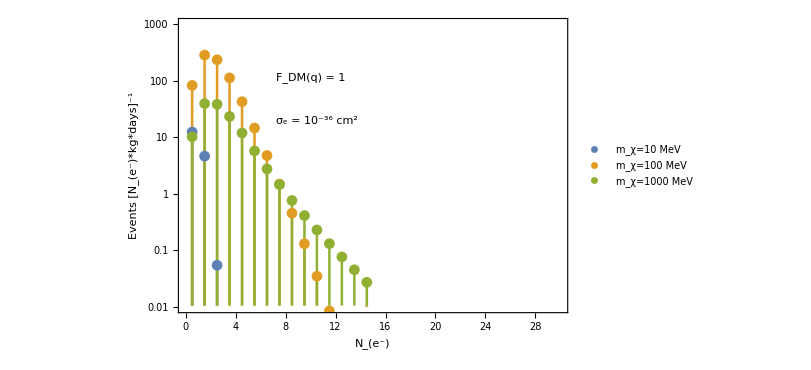

```mathematica
N12=Legended[Legended[ListLogPlot[{PoluNra1,PoluNra2,PoluNra3},PlotRange->{{0,30},{10^-2,1000}},PlotLegends->Placed[LineLegend[{"m_χ=10 MeV","m_χ=100 MeV","m_χ=1000 MeV"},LegendLayout->"Column"],{Scaled[{0.56,0.40}],{0,0.5}}], ImageSize->600,Frame->True,Background->White,FrameLabel->{"N_(e^-)","Events [N_(e^-)*kg*days]^-1"},PlotStyle->Thickness[0.005],Filling->Axis,FillingStyle->Thickness[0.003],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]],Placed[Text["σ_e = 10^-36 cm^2"],{Scaled[{0.25,0.65}],{0,0.5}}]],Placed[Text["F_DM(q) = 1"],{Scaled[{0.25,0.80}],{0,0.5}}]]
```

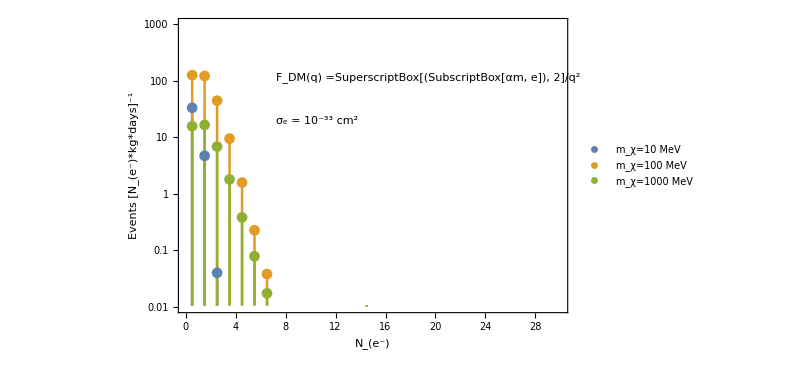

```mathematica
N13=Legended[Legended[ListLogPlot[{PoluNraF1,PoluNraF2,PoluNraF3},PlotRange->{{0,30},{10^-2,1000}},PlotLegends->Placed[LineLegend[{"m_χ=10 MeV","m_χ=100 MeV","m_χ=1000 MeV"},LegendLayout->"Column"],{Scaled[{0.56,0.40}],{0,0.5}}], ImageSize->600,Frame->True,Background->White,FrameLabel->{"N_(e^-)","Events [N_(e^-)*kg*days]^-1"},PlotStyle->Thickness[0.005],Filling->Axis,FillingStyle->Thickness[0.003],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]],Placed[Text["σ_e = 10^-33 cm^2"],{Scaled[{0.25,0.65}],{0,0.5}}]],Placed[Text["F_DM(q) =SuperscriptBox[(SubscriptBox[αm, e]), 2]/q^2"],{Scaled[{0.25,0.80}],{0,0.5}}]]
```

```mathematica
10.Rate from DM mass with fixed number of ionized electrons
```

```mathematica
Monitor[Ridm1=Table[{10^x,NIntegrate[Inert2p[10^x,Eer,0.5,q1]+Inert3p[10^x,Eer,0.5,q1]+Inert3s[10^x,Eer,0.5,q1],{q1,0.01,6000},{Eer,0.01,600},PrecisionGoal->2,MinRecursion->2]},{x,0.5,3.5,0.2}],x];
Monitor[Ridm2=Table[{10^x,NIntegrate[Inert2p[10^x,Eer,1.5,q1]+Inert3p[10^x,Eer,1.5,q1]+Inert3s[10^x,Eer,1.5,q1],{q1,0.01,6000},{Eer,0.01,600},PrecisionGoal->2,MinRecursion->2]},{x,0.5,3.5,0.2}],x];
Monitor[Ridm3=Table[{10^x,NIntegrate[Inert2p[10^x,Eer,2.5,q1]+Inert3p[10^x,Eer,2.5,q1]+Inert3s[10^x,Eer,2.5,q1],{q1,0.01,6000},{Eer,0.01,600},PrecisionGoal->2,MinRecursion->2]},{x,0.5,3.5,0.2}],x];
Monitor[Ridm4=Table[{10^x,NIntegrate[Inert2p[10^x,Eer,3.5,q1]+Inert3p[10^x,Eer,3.5,q1]+Inert3s[10^x,Eer,3.5,q1],{q1,0.01,6000},{Eer,0.01,600},PrecisionGoal->2,MinRecursion->2]},{x,0.5,3.5,0.2}],x];
```

```mathematica
Monitor[RidmF1=Table[{10^x,NIntegrate[Inert2pF[10^x,Eer,0.5,q1]+Inert3pF[10^x,Eer,0.5,q1]+Inert3sF[10^x,Eer,0.5,q1],{q1,0.01,6000},{Eer,0.01,600},PrecisionGoal->2,MinRecursion->2]},{x,0.5,3.5,0.07}],x];
```

```mathematica
Monitor[RidmF2=Table[{10^x,NIntegrate[Inert2pF[10^x,Eer,1.5,q1]+Inert3pF[10^x,Eer,1.5,q1]+Inert3sF[10^x,Eer,1.5,q1],{q1,0.01,6000},{Eer,0.01,600},PrecisionGoal->2,MinRecursion->2]},{x,0.5,3.5,0.2}],x];
Monitor[RidmF3=Table[{10^x,NIntegrate[Inert2pF[10^x,Eer,2.5,q1]+Inert3pF[10^x,Eer,2.5,q1]+Inert3sF[10^x,Eer,2.5,q1],{q1,0.01,6000},{Eer,0.01,600},PrecisionGoal->2,MinRecursion->2]},{x,0.5,3.5,0.2}],x];
Monitor[RidmF4=Table[{10^x,NIntegrate[Inert2pF[10^x,Eer,3.5,q1]+Inert3pF[10^x,Eer,3.5,q1]+Inert3sF[10^x,Eer,3.5,q1],{q1,0.01,6000},{Eer,0.01,600},PrecisionGoal->2,MinRecursion->2]},{x,0.5,3.5,0.2}],x];
```

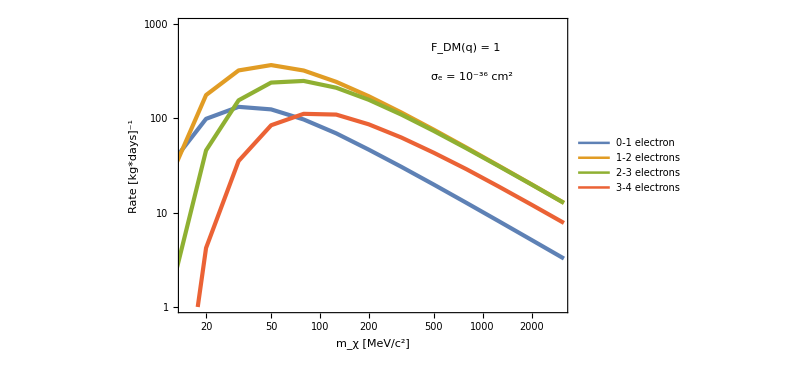

```mathematica
N14=Legended[Legended[ListLogLogPlot[{Ridm1,Ridm2,Ridm3,Ridm4},Joined->True,PlotRange->{{15,3000},{1,1000}},PlotLegends->Placed[LineLegend[{"0-1 electron","1-2 electrons","2-3 electrons","3-4 electrons"},LegendLayout->"Column"],{Scaled[{0.20,0.25}],{0,0.5}}], ImageSize->600,Frame->True,Background->White,FrameLabel->{"m_χ [MeV/c^2]","Rate [kg*days]^-1"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]],Placed[Text["σ_e = 10^-36 cm^2"],{Scaled[{0.65,0.80}],{0,0.5}}]],Placed[Text["F_DM(q) = 1"],{Scaled[{0.65,0.90}],{0,0.5}}]]
```

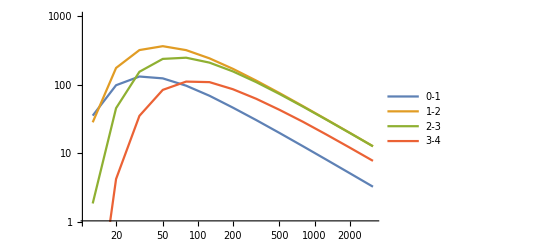

```mathematica
ListLogLogPlot[{Ridm1,Ridm2,Ridm3,Ridm4},PlotLegends->{"0-1","1-2","2-3","3-4"},Joined->True,PlotRange->{1,1000}]
```

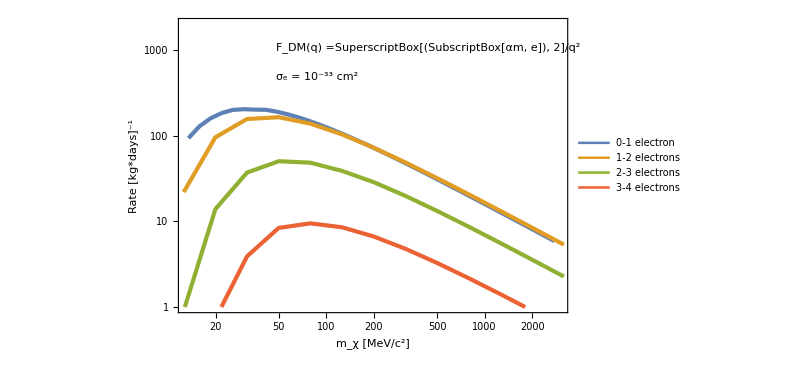

```mathematica
N15=Legended[Legended[ListLogLogPlot[{RidmF1,RidmF2,RidmF3,RidmF4},Joined->True,PlotRange->{{13,3000},{1,2000}},PlotLegends->Placed[LineLegend[{"0-1 electron","1-2 electrons","2-3 electrons","3-4 electrons"},LegendLayout->"Column"],{Scaled[{0.65,0.75}],{0,0.5}}], ImageSize->600,Frame->True,Background->White,FrameLabel->{"m_χ [MeV/c^2]","Rate [kg*days]^-1"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]],Placed[Text["σ_e = 10^-33 cm^2"],{Scaled[{0.25,0.80}],{0,0.5}}]],Placed[Text["F_DM(q) =SuperscriptBox[(SubscriptBox[αm, e]), 2]/q^2"],{Scaled[{0.25,0.90}],{0,0.5}}]]
```

```mathematica
11.Constraints on the scattering cross section of DM particles by electrons
```

```mathematica
Sigma[mmx_,Ne_]:=(2.3*10^(-36))/(NIntegrate[Inert2p[mmx,Eer,Ne,q1]+Inert3p[mmx,Eer,Ne,q1]+Inert3s[mmx,Eer,Ne,q1],{q1,0.01,6000},{Eer,0.01,600},PrecisionGoal->2,MinRecursion->2]);
SigmaF[mmx_,Ne_]:=(2.3*10^(-33))/(NIntegrate[Inert2pF[mmx,Eer,Ne,q1]+Inert3pF[mmx,Eer,Ne,q1]+Inert3sF[mmx,Eer,Ne,q1],{q1,0.01,6000},{Eer,0.01,600},PrecisionGoal->2,MinRecursion->2]);
```

```mathematica
Monitor[Sig1=Table[{10^x,Sigma[10^x,0.5]},{x,0.5,3.5,0.2}],x];
Monitor[Sig2=Table[{10^x,Sigma[10^x,1.5]},{x,0.5,3.5,0.2}],x];
Monitor[Sig3=Table[{10^x,Sigma[10^x,2.5]},{x,0.5,3.5,0.2}],x];
Monitor[Sig4=Table[{10^x,Sigma[10^x,3.5]},{x,0.5,3.5,0.2}],x];
```

```mathematica
Monitor[SigF1=Table[{10^x,SigmaF[10^x,0.5]},{x,0.5,3.5,0.02}],x];
```

```mathematica
Monitor[SigF2=Table[{10^x,SigmaF[10^x,1.5]},{x,0.5,3.5,0.2}],x];
Monitor[SigF3=Table[{10^x,SigmaF[10^x,2.5]},{x,0.5,3.5,0.2}],x];
Monitor[SigF4=Table[{10^x,SigmaF[10^x,3.5]},{x,0.5,3.5,0.2}],x];
```

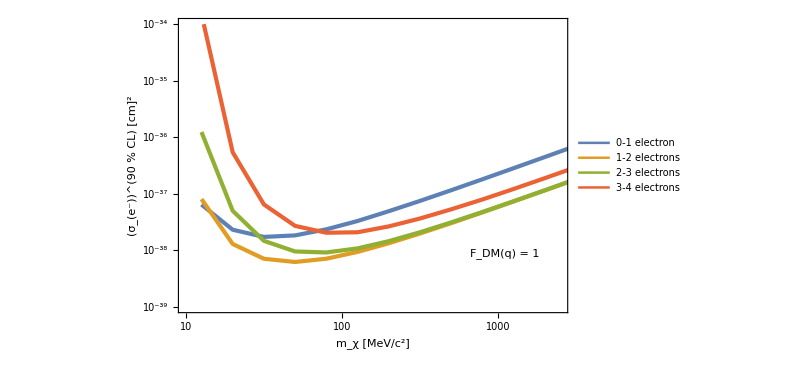

```mathematica
N16=Legended[ListLogLogPlot[{Sig1,Sig2,Sig3,Sig4},Joined->True,PlotRange->{{10,10^3.4},{10^-39,10^-34}},PlotLegends->Placed[LineLegend[{"0-1 electron","1-2 electrons","2-3 electrons","3-4 electrons"},LegendLayout->"Column"],{Scaled[{0.40,0.65}],{0,0.5}}], ImageSize->600,Frame->True,Background->White,FrameLabel->{"m_χ [MeV/c^2]","(σ_(e^-))^(90  % CL) [cm]^2"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]],Placed[Text["F_DM(q) = 1"],{Scaled[{0.75,0.20}],{0,0.5}}]]
```

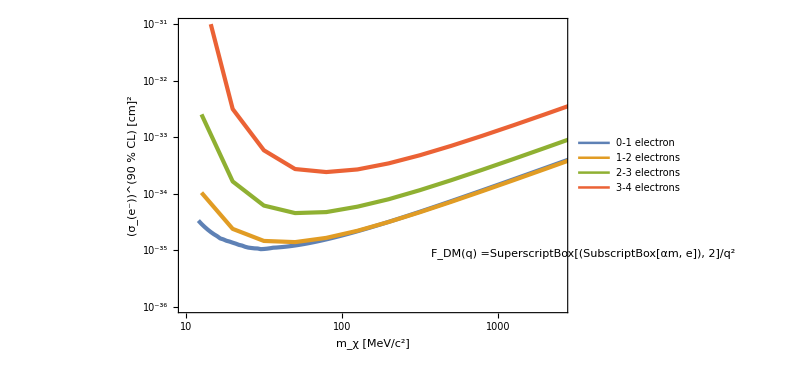

```mathematica
N17=Legended[ListLogLogPlot[{SigF1,SigF2,SigF3,SigF4},Joined->True,PlotRange->{{10,10^3.4},{10^-36,10^-31}},PlotLegends->Placed[LineLegend[{"0-1 electron","1-2 electrons","2-3 electrons","3-4 electrons"},LegendLayout->"Column"],{Scaled[{0.30,0.75}],{0,0.5}}], ImageSize->600,Frame->True,Background->White,FrameLabel->{"m_χ [MeV/c^2]","(σ_(e^-))^(90  % CL) [cm]^2"},PlotStyle->Thickness[0.005],GridLines->Automatic,FrameStyle->Directive[Black,Dashing],BaseStyle->{"Bold",FontSize->16},FrameStyle->Directive[Black,Dashing]],Placed[Text["F_DM(q) =SuperscriptBox[(SubscriptBox[αm, e]), 2]/q^2"],{Scaled[{0.65,0.20}],{0,0.5}}]]
```

```mathematica
12.Code to change exposure and redraw the plots
```

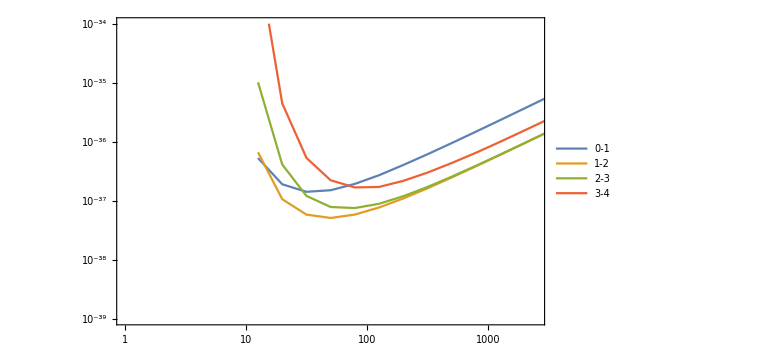

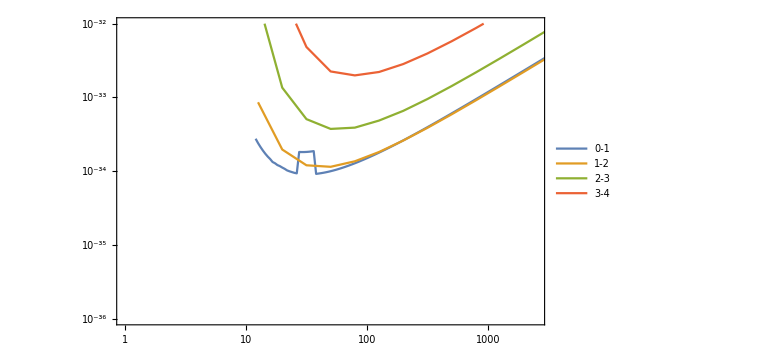

```mathematica
NovExp=2032;
NewSig1=Sig1;
NewSig2=Sig2;
NewSig3=Sig3;
NewSig4=Sig4;
NewSigF1=SigF1;
NewSigF2=SigF2;
NewSigF3=SigF3;
NewSigF4=SigF4;
NewSig1[[All,2]]=(ArExp/NovExp)*NewSig1[[All,2]];
NewSig2[[All,2]]=(ArExp/NovExp)*NewSig2[[All,2]];
NewSig3[[All,2]]=(ArExp/NovExp)*NewSig3[[All,2]];
NewSig4[[All,2]]=(ArExp/NovExp)*NewSig4[[All,2]];
NewSigF1[[All,2]]=(ArExp/NovExp)*NewSigF1[[All,2]];
NewSigF2[[All,2]]=(ArExp/NovExp)*NewSigF2[[All,2]];
NewSigF3[[All,2]]=(ArExp/NovExp)*NewSigF3[[All,2]];
NewSigF4[[All,2]]=(ArExp/NovExp)*NewSigF4[[All,2]];
ListLogLogPlot[{NewSig1,NewSig2,NewSig3,NewSig4},PlotLegends->{"0-1","1-2","2-3","3-4"},Joined->True,PlotRange->{{1,10^3.4},{10^-39,10^-34}},ImageSize->Large,Frame->True,PlotStyle->Thick]
ListLogLogPlot[{NewSigF1,NewSigF2,NewSigF3,NewSigF4},PlotLegends->{"0-1","1-2","2-3","3-4"},Joined->True,PlotRange->{{1,10^3.4},{10^-36,10^-32}},ImageSize->Large,Frame->True,PlotStyle->Thick]
```